```mathematica
ClearAll["Global`*"];
ta={0.1,0.12,0.4,0.46,0.8,0.82,1.2,1.24};
```

```mathematica
tb={0.8,0.85,-1.82,-1.9,0.5,0.54,-3.5,-3.3};
```

```mathematica
p[x_, A_,m_]:=(Sum[A[[i]]*x^(i-1),{i,m}]);
```

```mathematica
MNK[ta_,tb_,m_,n_,minx_,maxx_]:=(S=Array[s,{m,m}];X=Table[Sum[ta[[i]]^j/n,{i,n}],{j,0,2*(m-1)}]; Print["Sk:",X]; TA=Table[s[i,j]=X[[i+j-1]],{i,m},{j,m}];b=Table[Sum[ta[[i]]^j*tb[[i]]/n,{i,n}],{j,0,(m-1)}];Print["Bk: ",b];A=Inverse[TA].b;TT=Transpose[{ta,tb}];g1=ListPlot[TT];func=p[x,A,m];Print["Полученный многочлен: ", func];g2=Plot[p[x, A, m],{x,minx,maxx},PlotStyle->Red];Is=∑_(i=1)^n (p[TT[[i,1]], A, m]-TT[[i,2]])^2/n;fitted = Fit[TT,p[x, A, m],x]; Print["Отклонение: ",Is, "\nМногочлен, построенный с помощью функции Fit: ",fitted]; Show[g1,g2]);
```

Sk:{1.,0.6425,0.58575}

Bk: {-0.97875,-1.10865}

Полученный многочлен: 0.803757-2.77433 x

Отклонение: 1.70673
Многочлен, построенный с помощью функции Fit: 1. (0.803757-2.77433 x)

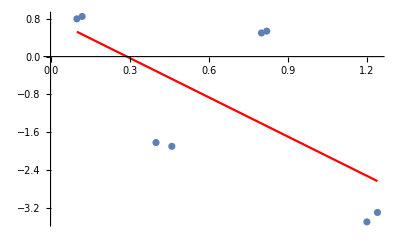

```mathematica
MNK[ta,tb,2,Length[ta],0.1,1.24]
```

Sk:{1.,0.6425,0.58575,0.607757,0.671277}

Bk: {-0.97875,-1.10865,-1.263}

Полученный многочлен: 0.0986326+0.66957 x-2.57376 x^2

Отклонение: 1.58401
Многочлен, построенный с помощью функции Fit: 1. (0.0986326+0.66957 x-2.57376 x^2)

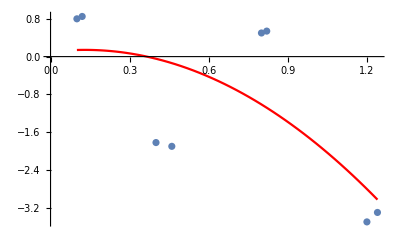

```mathematica
MNK[ta, tb, 3, Length[ta],0.1,1.24]
```

Sk:{1.,0.6425,0.58575,0.607757,0.671277,0.768655,0.900116}

Bk: {-0.97875,-1.10865,-1.263,-1.51066}

Полученный многочлен: 3.94839-35.604 x+66.6812 x^2-34.7344 x^3

Отклонение: 0.13432
Многочлен, построенный с помощью функции Fit: 1. (3.94839-35.604 x+66.6812 x^2-34.7344 x^3)

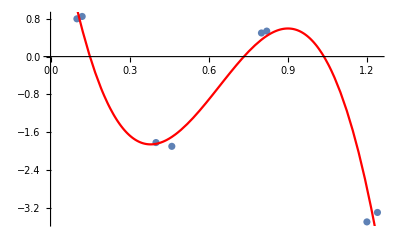

```mathematica
MNK[ta, tb, 4, Length[ta],0.1,1.24]
```

Sk:{1.,0.6425,0.58575,0.607757,0.671277,0.768655,0.900116,1.06948,1.28302}

Bk: {-0.97875,-1.10865,-1.263,-1.51066,-1.84275}

Полученный многочлен: 6.72635-72.9162 x+192.219 x^2-185.096 x^3+58.1649 x^4

Отклонение: 0.0789364
Многочлен, построенный с помощью функции Fit: 1. (6.72635-72.9162 x+192.219 x^2-185.096 x^3+58.1649 x^4)

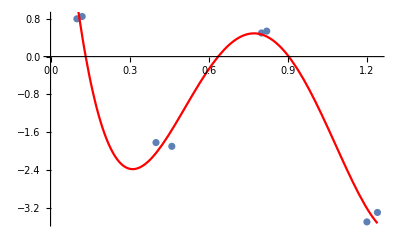

```mathematica
MNK[ta, tb, 5, Length[ta],0.1,1.24]
```

Sk:{1.,0.6425,0.58575,0.607757,0.671277,0.768655,0.900116,1.06948,1.28302,1.54922,1.87894}

Bk: {-0.97875,-1.10865,-1.263,-1.51066,-1.84275,-2.25965}

Полученный многочлен: -1.54543+47.9402 x-305.307 x^2+666.18 x^3-589.327 x^4+181.258 x^5

Отклонение: 0.0000165732
Многочлен, построенный с помощью функции Fit: 1. (-1.54543+47.9402 x-305.307 x^2+666.18 x^3-589.327 x^4+181.258 x^5)

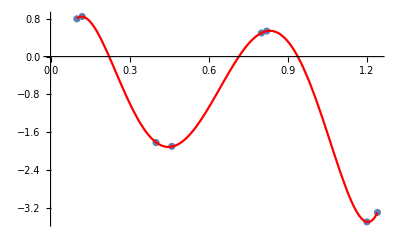

```mathematica
MNK[ta, tb, 6, Length[ta], 0.1,1.24]
```

Sk:{1.,0.6425,0.58575,0.607757,0.671277,0.768655,0.900116,1.06948,1.28302,1.54922,1.87894,2.28575,2.78652}

Bk: {-0.97875,-1.10865,-1.263,-1.51066,-1.84275,-2.25965,-2.77217}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,0.6425,0.58575,0.607757,0.671277,0.768655,0.900116},{0.6425,0.58575,0.607757,0.671277,0.768655,0.900116,1.06948},«4»,{0.900116,1.06948,1.28302,1.54922,1.87894,2.28575,2.78652}} may contain significant numerical errors.

Полученный многочлен: -1.70942+50.9768 x-324.341 x^2+719.746 x^3-662.763 x^4+229.136 x^5-11.8861 x^6

Отклонение: 3.77499×10^-6
Многочлен, построенный с помощью функции Fit: 1. (-1.70942+50.9768 x-324.341 x^2+719.746 x^3-662.763 x^4+229.136 x^5-11.8861 x^6)

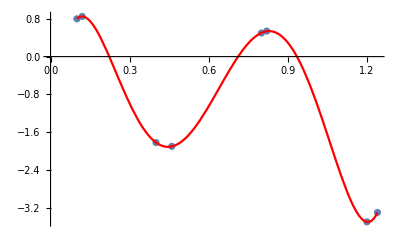

```mathematica
MNK[ta, tb, 7, Length[ta], 0.1,1.24]
```

```mathematica
(*Заканчиваем, так как отклонение слишком большое*)
```